```mathematica
(* initial vectors *)
a=Transpose[{7, 12}];
b=Transpose[{-4, 2}];
```

```mathematica
(* vector 'c' at t = 0, will be equal to the tensor product of vectors 'a' and 'b' *)
c0=Transpose[{a[[1]]*b[[1]], a[[1]]*b[[2]], a[[2]]*b[[1]], a[[2]]*b[[2]]}];
```

```mathematica
(* change matrix *)
h={{0, 0, 0, 0}, {0, -1, 1, 0}, {0, 1, -1, 0}, {0, 0, 0, 0}};
```

```mathematica
(* function describing the evolution of the system *)
evolution[x_]:=MatrixExp[I h x, c0];
```

```mathematica
(* moments of time *)
t=Range[1, 5, 0.0001];
```

```mathematica
(* form list containing displacement vector 'g' at each moment of time *)
g={};
Do [AppendTo[g, evolution[i]-c0], {i, t}];
```

```mathematica
(* finding the norm of 'g' vectors *)
gNorm={};
Do[AppendTo[gNorm, Norm[i, 2]], {i, g}];
```

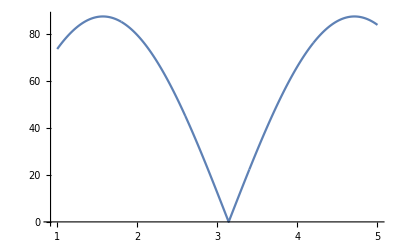

```mathematica
(* plot norms of 'g' *)
ListLinePlot[gNorm, DataRange->{t[[1]],t[[-1]]}]
```